```mathematica
NIntegrate[2Sqrt[1-x^2-y^2-z^2],{x,-1,1},{y,-Sqrt[1-x^2],Sqrt[1-x^2]},{z,-Sqrt[1-x^2-y^2],Sqrt[1-x^2-y^2]}]
```

4.9348

```mathematica
RegionPlot3D[Abs[x]+Abs[y]+Abs[z]<1,{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
Max[0,F[x,y,z]]
```

5

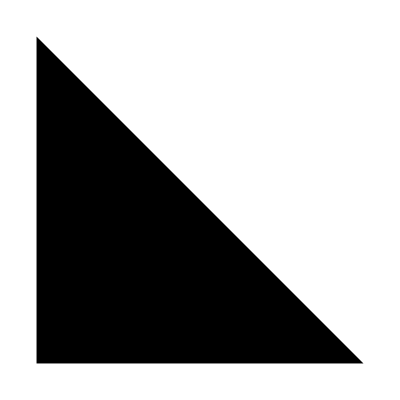

```mathematica
ConvexHullRegion[{
{1,2},
{2,1},
{1,1}
}]//Graphics
```

```mathematica
Polyhedron[…]//Graphics3D
```

-Graphics3D-

```mathematica
Graphics3D[Polyhedron[…]]
```

-Graphics3D-

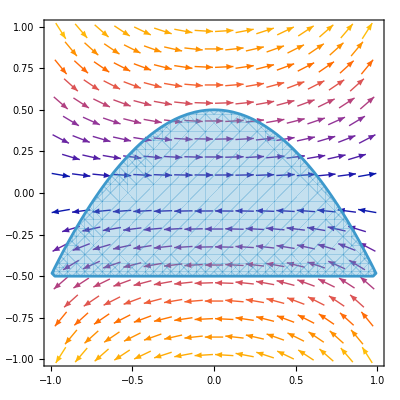

```mathematica
Show[
VectorPlot[{y Cos[x],x y^2},{x,-1,1},{y,-1,1}],
RegionPlot[-1/2≤y≤1/2-x^2,{x,-1,1},{y,-1,1}]
]
```